```mathematica
<<ErrorBarPlots`
```

```mathematica
(* Needs ErrorBarPlots package to render the error bars (or anything tbh) *)
```

Now, use converted data and process it.

```mathematica
(* Set up the experimental data needed. *)
```

```mathematica
experimentData = {
{
{1,0.15},
ErrorBar[0.01]
},{
{3,0.48},
ErrorBar[0.01]
},{
{5,0.81},
ErrorBar[0.01]
}
}
errorlessExpData={{1,0.15},{3,0.48},{5,0.81}} (* for FindFit (TODO: make it work when constrained by the error bars) *)
```

{{{1,0.15},ErrorBar[0.01]},{{3,0.48},ErrorBar[0.01]},{{5,0.81},ErrorBar[0.01]}}

{{1,0.15},{3,0.48},{5,0.81}}

```mathematica
(* Set up the model. We're expecting a linear fit, hence we're using the linear equation. Note that c should be negative valued (so -c instead of c).  *)
(* x represents N, c represents -x *)
```

```mathematica
a= λ/4
lineModel = a x + c
```

λ/4

c+(x λ)/4

```mathematica
lineFit=FindFit[errorlessExpData,lineModel, {λ,c},x]
```

{λ→0.66,c→-0.015}

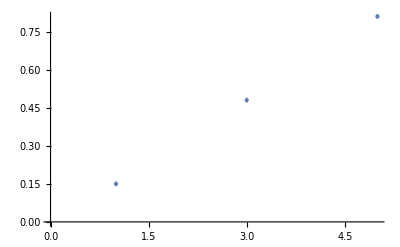

```mathematica
errorPlot=ErrorListPlot[experimentData,AxesOrigin->{0,0}, PlotStyle->{Thickness[Medium],PointSize[Medium]} ]
```

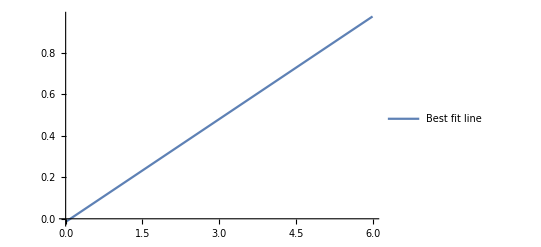

```mathematica
lineFitPlot=Plot[Evaluate[lineModel /. lineFit],{x,0,6}, PlotLegends->{"Best fit line"}, PlotStyle->Thickness[Medium]]
```

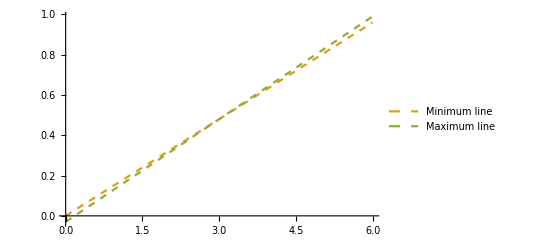

```mathematica
minMax=Plot[{0.16x,0.17x-0.03},{x,0,6},PlotStyle->{{Thickness[Small],Dashed,ColorData[97,2]},{Dashed,ColorData[97,3],Thickness[Medium]}},PlotLegends->{"Minimum line","Maximum line"}]
```

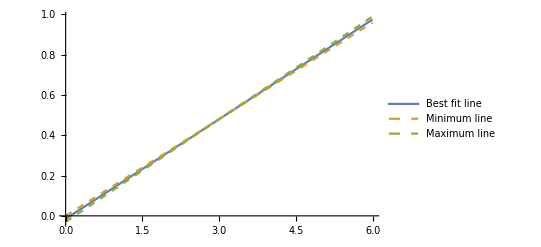

```mathematica
bestMinMax=Plot[{Evaluate[lineModel /. lineFit],0.16x,0.17x-0.03},{x,0,6},PlotStyle->{{Thickness[Medium],Normal}, {Thickness[Medium],Dashed}, {Thickness[Medium],Dashed}},PlotLegends->{"Best fit line", "Minimum line","Maximum line"}]
```

```mathematica
(* Combine the line plots with the plot of points with the error bars, and label the axes accordingly *)
```

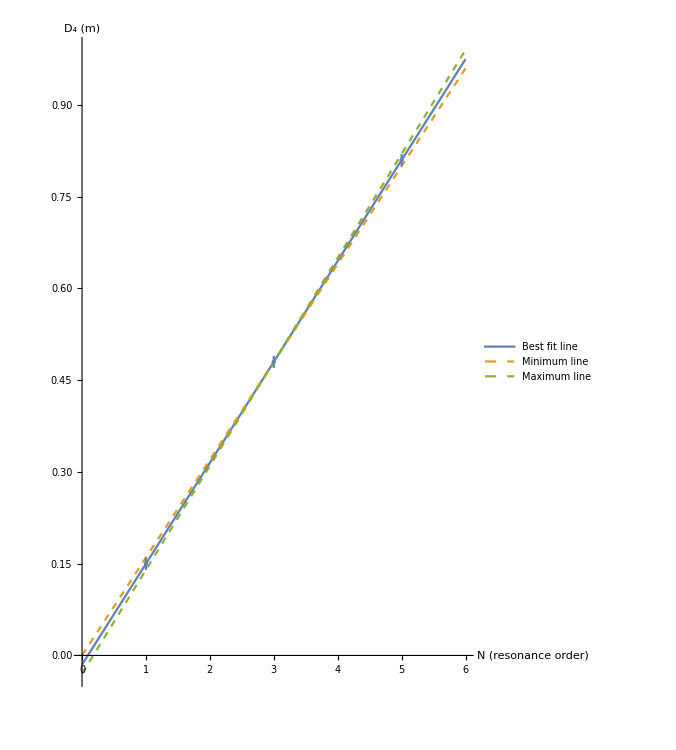

```mathematica
plotD4=Show[bestMinMax,errorPlot,AxesOrigin->{0,0},AspectRatio->1.5, AxesLabel-> {N " (resonance order)",Subscript[D, 4]"(m)"},ImageSize-> 500]
```

```mathematica
Export["plot.pdf", plotD4]
```

plot.pdf

Checking if the result is (at least roughly) equal to if we did not convert D to metres.

```mathematica
experimentDataCenti = {
{
{1,15},
ErrorBar[1]
},{
{3,48},
ErrorBar[1]
},{
{5,81},
ErrorBar[1]
}
}
errorlessExpDataCenti={{1,15},{3,48},{5,81}}
```

{{{1,15},ErrorBar[1]},{{3,48},ErrorBar[1]},{{5,81},ErrorBar[1]}}

{{1,15},{3,48},{5,81}}

λ/4

c+(x λ)/4

{λ→66.,c→-1.5}

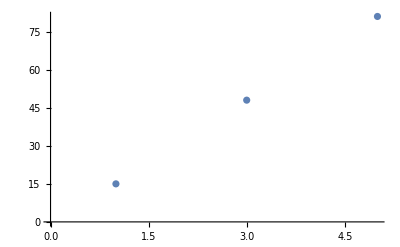

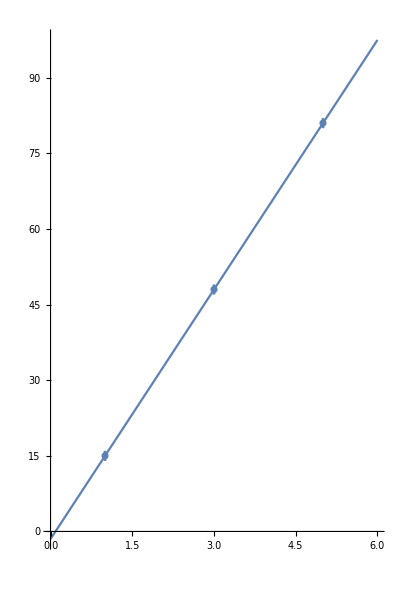

```mathematica
a= λ/4
lineModel = a x + c
lineFitCenti=FindFit[errorlessExpDataCenti,lineModel, {λ,c},x]
errorPlot=ErrorListPlot[experimentDataCenti,AxesOrigin->{0,0}, PlotStyle->Thickness[0.005]]
Show[Plot[Evaluate[lineModel /. lineFitCenti], {x, 0,6}],errorPlot,AxesOrigin->{0,0},AspectRatio->1.5]
```